```mathematica
m10=10;
m20=10;
fPBH0=10^-3;
mc0=19;
σ0=0.97;
σM0=0.006;
v0=10;
```

```mathematica
ψ[mc_,σ_,m_]:=1/(m*√(2*π*σ^2))*ⅇ^(-Log[m/mc]^2/(2*σ^2))
av[mc_,σ_]:=ⅇ^(σ^2/2) mc

F[x_]:=HypergeometricPFQ[{-1/2},{3/4,5/4},-9*x^2/16]
F[3]//N

NBar[m1_,m2_,fPBH_,mc_,σ_,σM_]:=(m1+m2)/av[mc,σ]*fPBH/(fPBH+σM)
avNBar[m1_,m2_,fPBH_,σM_]:=(m1+m2)*fPBH/(fPBH+σM)
avNBar[m1,m2,fPBH,σM]
```

3.0354

```mathematica
3.0353952615520314
```

(fPBH (m1+m2))/(fPBH+σM)

```mathematica
int[m1_?NumericQ,m2_?NumericQ,mc_?NumericQ,σ_?NumericQ,v_?NumericQ,fPBH_?NumericQ,σM_?NumericQ]:=-avNBar[m1,m2,fPBH,σM]*NIntegrate[ψ[mc,σ,m]/m*F[(m*v)/avNBar[m1,m2,fPBH,σM]],{m,0,∞}]

int[m10,m20,mc0,σ0,v0,fPBH0,σM0]
```

-10.0025

```mathematica
Gamma[21/37]//N
```

1.56858

```mathematica
S[m1_?NumericQ,m2_?NumericQ,fPBH_?NumericQ,mc_?NumericQ,σ_?NumericQ,σM_?NumericQ]:=ⅇ^(-NBar[m1,m2,fPBH,mc,σ,σM])/Gamma[21/37]*NIntegrate[v^(-16/37)*Exp[int[m1,m2,mc,σ,v,fPBH,σM]-(3*σM^2*v^2)/(10*fPBH^2)],{v,0,∞}]
```

```mathematica
S[5,5,fPBH0,mc0,σ0,σM0]//AbsoluteTiming
```

{45.2492,0.436222}

```mathematica
S[10,10,fPBH0,mc0,σ0,σM0]//AbsoluteTiming
```

{40.8945,0.365945}

```mathematica
S[20,20,fPBH0,mc0,σ0,σM0]//AbsoluteTiming
```

{32.8458,0.252212}

```mathematica
S[30,30,fPBH0,mc0,σ0,σM0]//AbsoluteTiming
```

{28.4379,0.17222}

```mathematica
S[40,40,fPBH0,mc0,σ0,σM0]//AbsoluteTiming
```

{27.3669,0.117179}

```mathematica
S[50,50,fPBH0,mc0,σ0,σM0]//AbsoluteTiming
```

{25.2519,0.0795874}

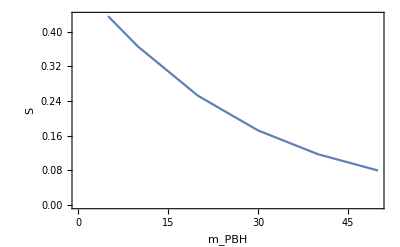

```mathematica
ListPlot[{{5,0.4362215210088267},{10,0.36594532847627204},{20,0.25221168596625226},{30,0.17221968614931793},{40,0.11717884890741737},{50,0.07958739645480131}},Joined->True,FrameLabel->{"m_PBH","S"},Frame->True]
```

```mathematica
NBar[m10,m20,fPBH0,mc0,σ0,σM0]
-avNBar[m10,m20,fPBH0,σM0]
NIntegrate[ψ[mc0,σ0,m]/m*F[(m*v0)/avNBar[m10,m20,fPBH0,σM0]],{m,0,∞}]
```

0.101088

-3.33333

3.00102

```mathematica
Integrate[ψ[mc,σ,m],{m,0,∞},Assumptions->σ>0&&mc>0]
```

1

```mathematica
Integrate[ψ[mc,σ,m]*m,{m,0,∞},Assumptions->σ>0&&mc>0]
```

ⅇ^(σ^2/2) mc

3.0354